# Interference between initial- and final-state emission

## Load FeynCalc

```mathematica
description="Learning FeynCalc through examples.";
If[ $FrontEnd === Null,
	$FeynCalcStartupMessages = False;
	Print[description];
];
If[ $Notebooks === False,
	$FeynCalcStartupMessages = False
];
$LoadAddOns={"FeynArts","FeynHelpers"};
<<FeynCalc`
$FAVerbose=0;

FCCheckVersion[9,3,1];
(FAPatch[PatchModelsOnly->True];)
```

FeynCalc 10.1.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples. The PDF-version of the manual can be downloaded here.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.12 (24 May 2024) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 2.0.0 (). For help, use the online documentation, visit the forum and have a look at the supplied examples.The PDF-version of the manual can be downloaded here.

If you use FeynHelpers in your research, please evaluate FeynHelpersHowToCite[] to learn how to cite this work.

Successfully patched FeynArts.

```mathematica
$KeepLogDivergentScalelessIntegrals = True;
```

```mathematica
$ToolsRoot=ParentDirectory[NotebookDirectory[]];
AppendTo[$Path,FileNameJoin[{$ToolsRoot,"Include"}]];
<<Tools`
<<PrettyNotation`
```

```mathematica
MakeBoxes[p1,TraditionalForm]:=SubscriptBox["p","1"];
MakeBoxes[p2,TraditionalForm]:=SubscriptBox["p","2"];
MakeBoxes[k1,TraditionalForm]:=SubscriptBox["k","1"];
MakeBoxes[k2,TraditionalForm]:=SubscriptBox["k","2"];
MakeBoxes[m1,TraditionalForm]:=SubscriptBox["m","1"];
MakeBoxes[m2,TraditionalForm]:=SubscriptBox["m","2"];
MakeBoxes[m3,TraditionalForm]:=SubscriptBox["m","3"];
MakeBoxes[μZ,TraditionalForm]:=SubscriptBox["μ","Z"];
MakeBoxes[ΓZ,TraditionalForm]:=SubscriptBox["Γ","Z"];
MakeBoxes[x0,TraditionalForm]:=SubscriptBox["x","0"];
MakeBoxes[x1,TraditionalForm]:=SubscriptBox["x","1"];
MakeBoxes[x2,TraditionalForm]:=SubscriptBox["x","2"];
MakeBoxes[xγ,TraditionalForm]:=SubscriptBox["x","γ"];
MakeBoxes[u1,TraditionalForm]:=SubscriptBox["u","1"];
MakeBoxes[u2,TraditionalForm]:=SubscriptBox["u","2"];
MakeBoxes[uγ,TraditionalForm]:=SubscriptBox["u","γ"];
MakeBoxes[z1,TraditionalForm]:=SubscriptBox["z","1"];
MakeBoxes[z2,TraditionalForm]:=SubscriptBox["z","2"];
MakeBoxes[zγ,TraditionalForm]:=SubscriptBox["z","γ"];
MakeBoxes[a1,TraditionalForm]:=SubscriptBox["a","1"];
MakeBoxes[a2,TraditionalForm]:=SubscriptBox["a","2"];
MakeBoxes[aγ,TraditionalForm]:=SubscriptBox["a","γ"];
MakeBoxes[β1,TraditionalForm]:=SubscriptBox["β","1"];
MakeBoxes[β2,TraditionalForm]:=SubscriptBox["β","2"];
MakeBoxes[xp,TraditionalForm]:=SuperscriptBox["x","+"];
MakeBoxes[xm,TraditionalForm]:=SuperscriptBox["x","-"];
MakeBoxes[λs,TraditionalForm]:=SubscriptBox["λ","s"];
MakeBoxes[λQ,TraditionalForm]:=SubscriptBox["λ","Q"];
MakeBoxes[c1,TraditionalForm]:=SubscriptBox["c","1"];
MakeBoxes[c2,TraditionalForm]:=SubscriptBox["c","2"];
```

## Draw diagrams

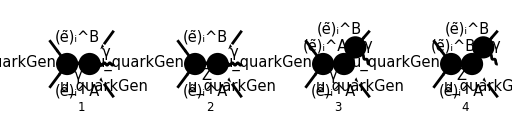

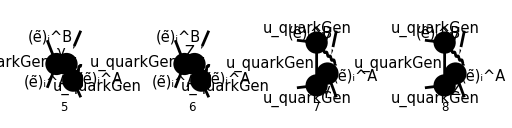

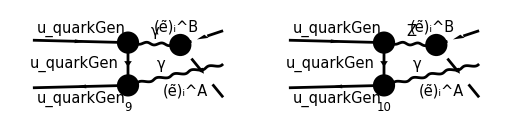

```mathematica
diags[0]=InsertFields[
CreateTopologies[0,2->3],
{F[3,{quarkGen}],-F[3,{quarkGen}]}->{-S[12,{B,i}],V[1],S[12,{A,i}]},
Model->MSSM,
InsertionLevel->{Classes},
ExcludeParticles->{
S[1|2|3|4|5|6],
V[3],
F[11|12],
S[11|13|14]
}
];
Paint[
diags[0],
ColumnsXRows->{4,1},
SheetHeader->None,
Numbering->Simple,
ImageSize->{512,128}
];
```

## Preliminaries

```mathematica
myAssumptions={
m1∈PositiveReals,
m2∈PositiveReals,
SMP["m_Z"]∈PositiveReals,
ΓZ∈PositiveReals,
s∈PositiveReals,
Q∈PositiveReals,
0<=y<=1,
0<z<=1,
0<=Y<=1,
0<=Z<1,
0<=xpxm,
-1<xm<xp<1,
xm<=x<=xp,
D>4
};
```

```mathematica
mZtoμZ[expr_]:=ReplaceAll[expr,SMP["m_Z"]->μZ]
photonPol[μ_]:=ChangeDimension[PolarizationVector[k,μ,Transversality->True],D]
photonPolConj[μ_]:=Conjugate[ChangeDimension[PolarizationVector[k,μ,Transversality->True],D]]
```

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(s z-m1^2-m2^2)/2;
```

## Amplitudes

```mathematica
Mlist[0]=FCFAConvert[
CreateFeynAmp[diags[0]],
IncomingMomenta->{p1,p2},
OutgoingMomenta->{k1,k,k2},
LorentzIndexNames->{μ,ν,ρ,σ},
Contract->False,
TransversePolarizationVectors->{k},
List->True,
SMP->True,
DropSumOver->True,
UndoChiralSplittings->True,
ChangeDimension->D
]/.{MQU[quarkGen]->0,MSf[B,2,i]->m1,MSf[A,2,i]->m2}//ZSimplify//mZtoμZ
```

{-(2 ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) g^μρ (ε^*)^μ(k) g^νρ e^2)/(k+k_1+k_2)^2,-(2 ⅈ Z_l_i^AB (φ(-p_2)).(2 ⅈ (Z_q_R γ^ν.(γ̄)^6+Z_q_L γ^ν.(γ̄)^7) e δ_Col1Col2)/((cos(θ_W)) (sin(θ_W))).(φ(p_1)) g^μρ (ε^*)^μ(k) g^νρ e^2)/(((k+k_1+k_2)^2-μ_Z^2) (cos(θ_W)) (sin(θ_W))),-(ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) (-k-2 k_1)^μ (ε^*)^μ(k) g^νρ (k+k_1-k_2)^ρ e^2)/((k+k_1+k_2)^2 ((-k-k_1)^2-m_2^2)),-(ⅈ Z_l_i^AB (φ(-p_2)).(2 ⅈ (Z_q_R γ^ν.(γ̄)^6+Z_q_L γ^ν.(γ̄)^7) e δ_Col1Col2)/((cos(θ_W)) (sin(θ_W))).(φ(p_1)) (-k-2 k_1)^μ (ε^*)^μ(k) g^νρ (k+k_1-k_2)^ρ e^2)/(((-k-k_1)^2-m_1^2) ((k+k_1+k_2)^2-μ_Z^2) (cos(θ_W)) (sin(θ_W))),-(ⅈ (φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(φ(p_1)) IndexDelta(A,B) (-k-2 k_2)^μ (ε^*)^μ(k) g^νρ (k-k_1+k_2)^ρ e^2)/((k+k_1+k_2)^2 ((k+k_2)^2-m_2^2)),-(ⅈ Z_l_i^AB (φ(-p_2)).(2 ⅈ (Z_q_R γ^ν.(γ̄)^6+Z_q_L γ^ν.(γ̄)^7) e δ_Col1Col2)/((cos(θ_W)) (sin(θ_W))).(φ(p_1)) (-k-2 k_2)^μ (ε^*)^μ(k) g^νρ (k-k_1+k_2)^ρ e^2)/(((k+k_2)^2-m_2^2) ((k+k_1+k_2)^2-μ_Z^2) (cos(θ_W)) (sin(θ_W))),((φ(-p_2)).(-2/3 ⅈ γ^ν e δ_Col1Col2).(γ·(k_1+k_2-p_2)).(-2/3 ⅈ γ^μ e).(φ(p_1)) IndexDelta(A,B) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e)/((k_1+k_2)^2 (-k_1-k_2+p_2)^2),(Z_l_i^AB (φ(-p_2)).(2 ⅈ (Z_q_R γ^ν.(γ̄)^6+Z_q_L γ^ν.(γ̄)^7) e δ_Col1Col2)/((cos(θ_W)) (sin(θ_W))).(γ·(k_1+k_2-p_2)).(-2/3 ⅈ γ^μ e).(φ(p_1)) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e)/((-k_1-k_2+p_2)^2 ((k_1+k_2)^2-μ_Z^2) (cos(θ_W)) (sin(θ_W))),((φ(-p_2)).(-2/3 ⅈ γ^μ e δ_Col1Col2).(γ·(k-p_2)).(-2/3 ⅈ γ^ν e).(φ(p_1)) IndexDelta(A,B) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e)/((k_1+k_2)^2 (p_2-k)^2),(Z_l_i^AB (φ(-p_2)).(-2/3 ⅈ γ^μ e δ_Col1Col2).(γ·(k-p_2)).(2 ⅈ (Z_q_R γ^ν.(γ̄)^6+Z_q_L γ^ν.(γ̄)^7) e)/((cos(θ_W)) (sin(θ_W))).(φ(p_1)) (ε^*)^μ(k) g^νρ (k_2-k_1)^ρ e)/((p_2-k)^2 ((k_1+k_2)^2-μ_Z^2) (cos(θ_W)) (sin(θ_W)))}

```mathematica
Mqγ[0]=(Mlist[0][[{7,9}]]//Total)(3/2SMP["e_Q"])^2;
MqZ[0]=(Mlist[0][[{8,10}]]//Total)3/2SMP["e_Q"];
Mq[0]=Mqγ[0]+MqZ[0]//Contract//FullSimplify//FCE//ReplaceAll[#,FAD[p2-k1-k2]->FAD[p1-k]]&//FeynAmpDenominatorExplicit//ReplaceAll[#,k2->p1+p2-k1-k]&//DiracSimplify//FullSimplify
```

(e^3 e_Q δ_Col1Col2 (2 s z Z_l_i^AB (-2 (k·p_1) (p_2·ε^*(k)) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))+(k·p_2) (2 (p_1·ε^*(k)) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))-Z_q_L (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))-Z_q_R (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))+(k·p_1) Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^7.(φ(p_1))+(k·p_1) Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(γ̄)^6.(φ(p_1)))-e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (s z-μ_Z^2) ((k·p_1) (φ(-p_2)).(γ·ε^*(k)).(γ·k).(γ·k_1).(φ(p_1))-(k·p_2) (φ(-p_2)).(γ·k_1).(γ·k).(γ·ε^*(k)).(φ(p_1))+2 ((k·p_2) (p_1·ε^*(k))-(k·p_1) (p_2·ε^*(k))) (φ(-p_2)).(γ·k_1).(φ(p_1)))))/(s z (cos(θ_W))^2 (k·p_1) (k·p_2) (sin(θ_W))^2 (s z-μ_Z^2))

```mathematica
Mlγ[0]=(Mlist[0][[{3,5}]]//Total)3/2SMP["e_Q"]//FeynAmpDenominatorSplit//FCE//ReplaceAll[#,FAD[{-k-k1,m2}]->FAD[{-k-k1,m1}]]&;
MlZ[0]=Mlist[0][[{4,6}]]//Total;
Ml[0]=Mlγ[0]+MlZ[0]//Contract//ReplaceAll[#,k+k1+k2->p1+p2]&//FeynAmpDenominatorExplicit//DiracGammaExpand//FCE//ReplaceAll[#,GSD[k2]->GSD[p1+p2-k1-k]]&//DiracSimplify//FullSimplify
```

-((2 e^3 δ_Col1Col2 (2 s Z_l_i^AB (((k·k_2) (k_1·ε^*(k))-(k·k_1) (k_2·ε^*(k))) (Z_q_L (φ(-p_2)).(γ·k_1).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·k_1).(γ̄)^6.(φ(p_1)))+(k·k_2) (k_1·ε^*(k)) Z_q_L (φ(-p_2)).(γ·k).(γ̄)^7.(φ(p_1))+(k·k_2) (k_1·ε^*(k)) Z_q_R (φ(-p_2)).(γ·k).(γ̄)^6.(φ(p_1)))-e_Q (cos(θ_W))^2 (s-μ_Z^2) (sin(θ_W))^2 IndexDelta(A,B) ((k·k_2) (k_1·ε^*(k)) ((φ(-p_2)).(γ·k).(φ(p_1))+(φ(-p_2)).(γ·k_1).(φ(p_1)))-(k·k_1) (k_2·ε^*(k)) (φ(-p_2)).(γ·k_1).(φ(p_1)))))/(s (k·k_1) (k·k_2) (cos(θ_W))^2 (s-μ_Z^2) (sin(θ_W))^2))

```mathematica
M4γ[0]=Mlist[0][[1]]3/2SMP["e_Q"];
M4Z[0]=Mlist[0][[2]];
M4[0]=M4γ[0]+M4Z[0]//Contract//ReplaceAll[#,k1+k2+k->p1+p2]&//FeynAmpDenominatorExplicit//DiracSimplify//FullSimplify
```

(2 e^3 δ_Col1Col2 (2 s Z_l_i^AB (Z_q_L (φ(-p_2)).(γ·ε^*(k)).(γ̄)^7.(φ(p_1))+Z_q_R (φ(-p_2)).(γ·ε^*(k)).(γ̄)^6.(φ(p_1)))+e_Q (cos(θ_W))^2 (μ_Z^2-s) (sin(θ_W))^2 IndexDelta(A,B) (φ(-p_2)).(γ·ε^*(k)).(φ(p_1))))/(s (cos(θ_W))^2 (s-μ_Z^2) (sin(θ_W))^2)

## Interferences

```mathematica
FCClearScalarProducts[];
SPD[p1]=SPD[p2]=SPD[k]=0;
SPD[k1]=m1^2;
SPD[k2]=m2^2;
SPD[p1,p2]=s/2;
SPD[k1,k2]=(s z-m1^2-m2^2)/2;
SPD[k1,k]=s/4Z(1-x);
SPD[k2,k]=s/4Z(1+x);
SPD[p1,k]=s/2Z Y;
SPD[p2,k]=s/2Z y;
SPD[p1,k1]=s/4(y+z Y+(2Sqrt[y]Sqrt[Y]Sqrt[z]Sqrt[xpxm]cϕ+z Y(x+2(mt1^2-mt2^2))-x y));
SPD[p1,k2]=s/4(y+z Y-(2Sqrt[y]Sqrt[Y]Sqrt[z]Sqrt[xpxm]cϕ+z Y(x+2(mt1^2-mt2^2))-x y));
SPD[p2,k1]=s/4(Y+z y+(-2Sqrt[y]Sqrt[Y]Sqrt[z]Sqrt[xpxm]cϕ+z y(x+2(mt1^2-mt2^2))-x Y));
SPD[p2,k2]=s/4(Y+z y-(-2Sqrt[y]Sqrt[Y]Sqrt[z]Sqrt[xpxm]cϕ+z y(x+2(mt1^2-mt2^2))-x Y));
```

```mathematica
Mq4[0]=ComplexConjugate[Mq[0],Conjugate->{μZ}]M4[0]//DoPolarizationSums[#,k,0]&//FermionSpinSum[#,ExtraFactor->1/(4SUNN^2)]&//DiracSimplify//FCE//ReplaceAll[#,GAD[5]->0]&//DiracSimplify//ReplaceAll[#,{m1->Sqrt[s z]mt1,m2->Sqrt[s z]mt2}]&//FullSimplify[#,Assumptions->myAssumptions]&
Mq4[1]=(Mq4[0]//ReplaceAll[#,Y->1-y]&//Collect2[#,{cϕ},IsolateNames->KK]&)(1-cϕ^2)^((D-5)/2)//Integrate[#,{cϕ,-1,1},Assumptions->myAssumptions]&
```

-(((D-2) e^6 e_Q δ_Col1Col2^2 (-2 cϕ (√(xpxm y^5 Y z)+2 √(xpxm y^3 Y^3 z)+√(xpxm y Y^5 z))+(x-1) y^3+(x-1) y^2 Y-(x-1) y (Y^2+1)-(x-1) Y (Y^2-1)) (e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) (e_Q (cos(θ_W))^2 (sin(θ_W))^2 (Abs[μ_Z]^4-s (Conjugate[(μ_Z)])^2+s z (s-μ_Z^2))-s Z_l_i^AB (Z_q_L+Z_q_R) (-(Conjugate[(μ_Z)])^2+2 s z-z μ_Z^2))+2 s^2 z (Z_l_i^AB)^2 (Z_q_L^2+Z_q_R^2)))/(2 N^2 s y Y z (cos(θ_W))^4 (s-μ_Z^2) (sin(θ_W))^4 (s z-(Conjugate[(μ_Z)])^2)))

0

```mathematica
Mql[0]=ComplexConjugate[Mq[0],Conjugate->{μZ}]Ml[0]//DoPolarizationSums[#,k,0]&//FermionSpinSum[#,ExtraFactor->1/(4SUNN^2)]&//DiracSimplify//FCE//ReplaceAll[#,GAD[5]->0]&//DiracSimplify//Collect2[#,{cϕ},IsolateNames->KK]&
Mql[1]=Mql[0](1-cϕ^2)^((D-5)/2)//Integrate[#,{cϕ,-1,1},Assumptions->myAssumptions]&
```

16 cϕ^3 KK(31070)-4 cϕ^2 KK(31074)+2 cϕ KK(31072)-KK(31076)

-(√π e^6 KK(20439) KK(31069) (D-3)/2 e_Q δ_Col1Col2^2 ((D-2) KK(31075) Z+4 KK(31073) s xpxm y Y z))/(2 KK(19235) KK(19236) KK(20300) KK(31067) N^2 s^2 y Y z Z^2 D/2 (cos(θ_W))^4 (sin(θ_W))^4)

```mathematica
Mql[2]=((Mql[1]//FRH)Z^2//ReplaceAll[#,Z->1-z]&)/Z^2//Simplify[#,Assumptions->myAssumptions]&//ReplaceAll[#,y+Y->1]&
```

-((√π e^6 (D-3)/2 e_Q (y-Y) δ_Col1Col2^2 (4 s xpxm y Y z (y (4 mt1^2 z-4 mt2^2 z+z-1)+4 mt1^2 Y z-4 mt2^2 Y z+x (y (z+3)+Y (z+3)+z-1)+Y z-Y-z+1)-(D-2) (z-1) (2 y Y (m_1^2 (2 x (mt1^2 z-mt2^2 z+3)+z (6 mt1^2-6 mt2^2-1)+x^2 (z+1)+1)-m_2^2 (x-1) (2 mt1^2 z-2 mt2^2 z+x z+x+z-1))+s (x-1) (-2 x y Y z (mt1^2 (2 y+2 Y-z-3)+mt2^2 (-2 y-2 Y+z+3))-y^2 (Y z (4 mt1^2-4 mt2^2+2)+Y+z-1)-y Y^2 (z (4 mt1^2-4 mt2^2+2)+1)+2 y Y z (mt1^2-mt2^2) (2 mt1^2 z-2 mt2^2 z+z+1)-y^3+y-(Y^2-1) (Y+z-1)))) (e_Q (cos(θ_W))^2 (sin(θ_W))^2 IndexDelta(A,B) ((Conjugate[(μ_Z)])^2 (s Z_l_i^AB (Z_q_L+Z_q_R)+e_Q (cos(θ_W))^2 (μ_Z^2-s) (sin(θ_W))^2)+s z (e_Q (cos(θ_W))^2 (s-μ_Z^2) (sin(θ_W))^2-(2 s-μ_Z^2) Z_l_i^AB (Z_q_L+Z_q_R)))+2 s^2 z (Z_l_i^AB)^2 (Z_q_L^2+Z_q_R^2)))/(2 N^2 s^2 (x-1) (x+1) y Y z Z^2 D/2 (cos(θ_W))^4 (s-μ_Z^2) (sin(θ_W))^4 (s z-(Conjugate[(μ_Z)])^2)))

```mathematica
Mql[3]=(Mql[2]//Collect2[#,{y,Y},IsolateNames->KK]&)(y Y)^((d-4)/2)//ReplaceAll[#,Y->1-y]&//Integrate[#,{y,0,1}]&
```

ConditionalExpression[0, Re(d)>2]

```mathematica
Mql[0]=ComplexConjugate[Mq[0],Conjugate->{μZ}]Ml[0]//DoPolarizationSums[#,k,0]&//FermionSpinSum[#,ExtraFactor->1/(4SUNN^2)]&//DiracSimplify//FCE//ReplaceAll[#,GAD[5]->0]&//DiracSimplify//ReplaceAll[#,y+Y->1]&//Collect2[#,{y,Y},IsolateNames->KK]&
```

(4 KK(41563) y^(5/2))/(√Y)+4 KK(41571) y^(3/2) √Y-(2 KK(41574) y^(3/2))/(√Y)-(KK(41572) y^3)/Y+(KK(41561) y^2)/Y-2 KK(41567) y^2+4 KK(41571) √y Y^(3/2)+(4 KK(41563) Y^(5/2))/(√y)-(2 KK(41574) Y^(3/2))/(√y)+(KK(41572) Y^3)/y-(KK(41561) Y^2)/y+(KK(41572) y)/Y+(2 KK(41560) √y)/(√Y)+4 KK(41565) √y √Y+(2 KK(41560) √Y)/(√y)-(KK(41572) Y)/y-KK(41569) y+(KK(41561))/y+2 KK(41567) Y^2-(KK(41561))/Y+KK(41569) Y

```mathematica
Mql[1]=(Mql[0]y Y//Collect2[#,{y,Y},IsolateNames->KK]&)(y Y)^((D-6)/2)//ReplaceAll[#,Y->1-y]&//Integrate[#,{y,0,1},Assumptions->myAssumptions]&
```

(√π cϕ 2^(3-D) e^6 KK(31069) (D-3)/2 e_Q √(xpxm/z) δ_Col1Col2^2 ((D+1) KK(20300) KK(41562) s+D KK(41570) s+(D-3) KK(41564) Z-D KK(41573) Z-2 (D-2) KK(44822)-3 KK(41570) s+KK(41573) Z))/(KK(19235) KK(19236) KK(20300) KK(31067) N^2 s^2 Z^2 D/2 (cos(θ_W))^4 (sin(θ_W))^4)

```mathematica
%//FRH//Collect2[#,{cϕ},IsolateNames->KK]&
```

cϕ^3 KK(48404)-cϕ KK(48402)